## basis su(8)

```mathematica
indices=Sort[Tuples[{1,2,3,4},3][[2;;]],Length[Select[#1,#==1&]]>Length[Select[#2,#==1&]]&];
```

```mathematica
paulis={IdentityMatrix[2],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
```

```mathematica
NFoldKron[index_]:= Fold[KroneckerProduct,paulis[[index[[1]]]],Map[paulis[[#]]&,index[[2;;]] ] ]
```

```mathematica
su8=(0.0+1.0 ⅈ)/Sqrt[2^3] NFoldKron/@indices;
```

```mathematica
projA[mat_]:=Chop[Total[Table[-Tr[N[mat.su8[[i]]]] su8[[i]],{i,1,36}]]]
```

## check validation data

```mathematica
dataOut=Import["/home/michael/Dropbox/Public/nnQCompile/su16/lstm/prediction_outputs.csv"];
```

```mathematica
dataValid=Import["/home/michael/Dropbox/Public/nnQCompile/su16/lstm/data_valid.csv"];
```

```mathematica
dataValid=Import["/Users/mswaddle/Dropbox/Public/nnQCompile/su16/lstm/data_valid.csv"];
```

Import::nffil: File not found during Import.

```mathematica
dataOut=Import["/Users/mswaddle/Dropbox/Public/nnQCompile/lstm/geod/prediction_outputs.csv"];
```

```mathematica
Manipulate[
Show[
ListLinePlot[
Transpose[Partition[dataOut[[i]],64]][[j]],PlotRange->All,PlotStyle->Blue],ListLinePlot[Transpose[Partition[dataValid[[2i-1]],64]][[j]] ,PlotStyle->Red],PlotRange->All],{i,1,Length[dataOut],1},{j,1,64,1}]
```

```mathematica
Export["u14_25.pdf",Show[
ListLinePlot[
Transpose[Partition[dataOut[[14]],64]][[25]],PlotRange->All,PlotStyle->Blue,
Frame->True,
FrameLabel->{{"",""},{i,"Components of Re(U_i)"}},FrameStyle->Directive[FontFamily->"Helvetica",Medium,Black],
FrameTicks->{{Automatic,None},{{2,4,6,8,10},None}}
],
ListLinePlot[
Transpose[Partition[dataValid[[2 14-1]],64]][[25]] ,PlotStyle->Red
]
]]
```

u14_25.pdf

```mathematica
Export["u34_40.pdf",Show[
ListLinePlot[
Transpose[Partition[dataOut[[34]],64]][[40]],PlotRange->All,PlotStyle->Blue,
Frame->True,
FrameLabel->{{"",""},{i,"Components of Re(U_i)"}},FrameStyle->Directive[FontFamily->"Helvetica",Medium,Black],
FrameTicks->{{Automatic,None},{{2,4,6,8,10},None}}
],
ListLinePlot[
Transpose[Partition[dataValid[[2 34-1]],64]][[40]] ,PlotStyle->Red
]
]]
```

u34_40.pdf

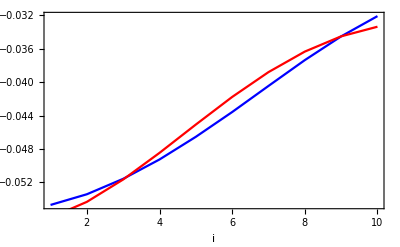

```mathematica
Show[
ListLinePlot[
Transpose[Partition[dataOut[[34]],64]][[40]],PlotRange->All,PlotStyle->Blue,
Frame->True,
FrameLabel->{{"",""},{i,"Components of Re(U_i)"}},FrameStyle->Directive[FontFamily->"Helvetica",Medium,Black],
FrameTicks->{{Automatic,None},{{2,4,6,8,10},None}}
],
ListLinePlot[
Transpose[Partition[dataValid[[2 34-1]],64]][[40]] ,PlotStyle->Red
]
]
```

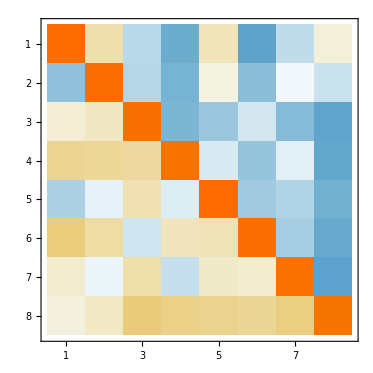

```mathematica
valid=MatrixPlot[Partition[Partition[dataValid[[1]],64][[1]],8],FrameStyle->Directive[Black,16,FontFamily->"Helvetica"]]
```

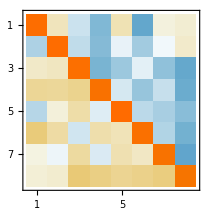

```mathematica
out=MatrixPlot[Partition[Partition[dataOut[[1]],64][[1]],8],FrameStyle->Directive[Black,16,FontFamily->"Helvetica"]]
```

```mathematica
Export["out.pdf",out]
```

out.pdf

```mathematica
Export["valid.pdf",valid]
```

valid.pdf

## generate approximate geodesic training data

```mathematica
nTraining = 100;
classifications=Reap[
Do[
(* setting initial conditions to be sparse *)
initCondPerp=RandomReal[{0,1},27 ];
(*initCondPerp=Map[If[RandomInteger[{1,10}]<5,#*0,#]&,initCondPerp]*);
initCondA=RandomReal[{0,1},36 ];
(*initCondA=Map[If[RandomInteger[{1,10}]<5,#*0,#]&,initCondA]*);
initCond=Join[initCondA,initCondPerp];

z0 = initCond.su8;
x0=IdentityMatrix[8];
h=0.1;
x1=x0;
UData=Reap[Do[
U=Chop[MatrixExp[h Chop[projA[ x0.z0.ConjugateTranspose[x0]]]]];
x1=U.x0;
x0=x1;
Sow[U];,
{i,0,Round[1/h]-1}]][[2]];

(* last exponentials come first because right mult, ie Subscript[x, n+1]= u Subscript[x, n]*)

x2=Dot@@Reverse[UData[[1]]];
Sow[{Reverse[Re[Flatten[Chop[UData]]]],Flatten[Re[Chop[x2]]]}];
,{nTraining}]
];
class=Flatten[Flatten[classifications[[2]],1],1];
```

```mathematica
Export["/Users/mswaddle/Dropbox/Public/nnQCompile/lstm/geod/data_training.csv",class]
```

/Users/mswaddle/Dropbox/Public/nnQCompile/lstm/geod/data_training.csv

```mathematica
Export["/Users/mswaddle/Dropbox/Public/nnQCompile/lstm/geod/data_valid.csv",class]
```

/Users/mswaddle/Dropbox/Public/nnQCompile/lstm/geod/data_valid.csv

```mathematica
11
```

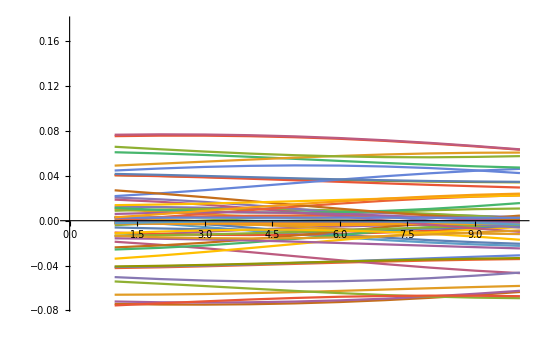

```mathematica
ListLinePlot[
Transpose[Partition[dataOut[[1]],64]]]
```